```mathematica
Clear[x];
```

```mathematica
Clear[y];
```

```mathematica
f1[t_,x_,y_]:=t*x- Sin[y]
f2[t_,x_,y_]:=Cos[t]*x-y Sin[x];
```

```mathematica
x[0]=.2;
```

```mathematica
y[0]=.2;
```

```mathematica
h=.05;
```

```mathematica
Do[{k11=h f1[h n,x[n],y[n]];
k12=h f2[h n,x[n],y[n]];
k21=h f1[h (n+1),x[n]+k11,y[n]+k12];
k22=h f2[h (n+1),x[n]+k11,y[n]+k12];
x[n+1]=x[n]+ .5(k11+k21),
y[n+1]=y[n]+.5(k12+k22)},{n,0,20}]
```

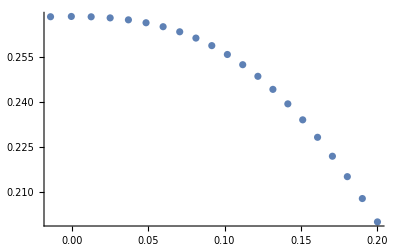

```mathematica
a=ListPlot[Table[{x[n],y[n]},{n,0,20}]]
```

```mathematica
N[x[2]]
```

0.180298

```mathematica
Clear[x];
```

```mathematica
Clear[y];
```

```mathematica
s=NDSolve[{x'[t]==t*x[t]-Sin[y[t]],y'[t]==Cos[t]*x[t]-y[t]Sin[x[t]],{x[0]==.2,y[0]==.2}},{x,y},{t,1}]
```

{{x→InterpolatingFunction[{{0., 1.}}, <>],y→InterpolatingFunction[{{0., 1.}}, <>]}}

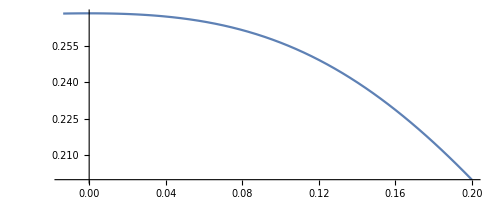

```mathematica
b=ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,1}]
```

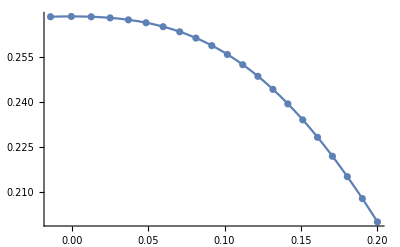

```mathematica
Show[a,b]
```

```mathematica
y[1]/.s
```

{0.26826}